The MassiveGraph.wl package needs:
- GraphGenerator.wl which is in the GitHub repository https://github.com/StefanoDeAngelis/SMEFT-operators
- HelicityVariable.wl which is in the GitHub repository https://github.com/StefanoDeAngelis/SpinorHelicity
The documentation for such packages are not available yet.

```mathematica
(*<<HelicityVariables`*)
(*<<GraphGenerator`*)
<<MassiveGraphs`
```

```mathematica
?IndependentSpinStructres
```

```mathematica
?UniformMassStructres
```

Momenta:  {2,0,0,0}

Graphs before momentum conservation:  {-Graphics-}

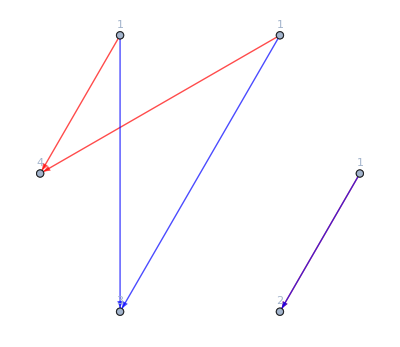
Graphs with momenta:  {-Graphics-}

Conditions:  {False,True}

True

No graph survided.

Momenta:  {0,2,0,0}

Graphs before momentum conservation:  {-Graphics-}

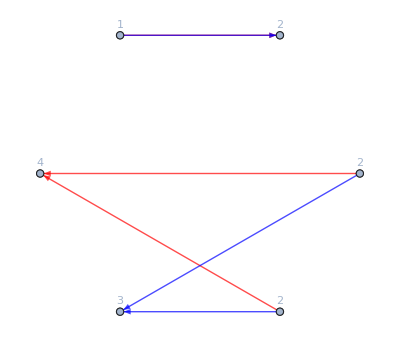
Graphs with momenta:  {-Graphics-}

Conditions:  {}

False

Graphs:  {-Graphics-}

Momenta:  {1,1,0,0}

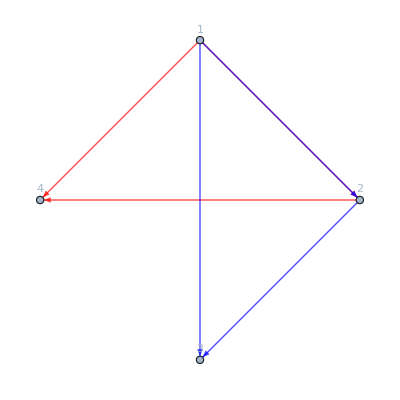
Graphs before momentum conservation:  {-Graphics-}

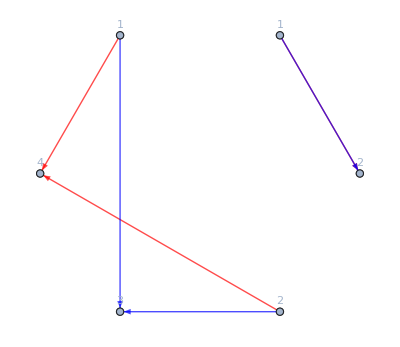
Graphs with momenta:  {-Graphics-}

Conditions:  {False,True}

True

No graph survided.

Momenta:  {1,0,1,0}

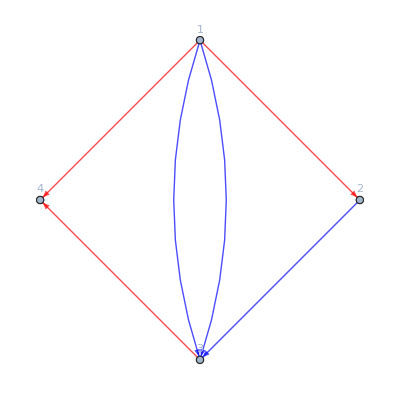
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

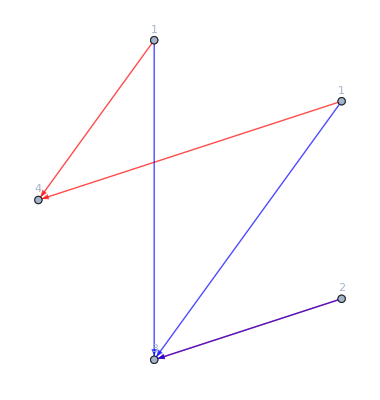
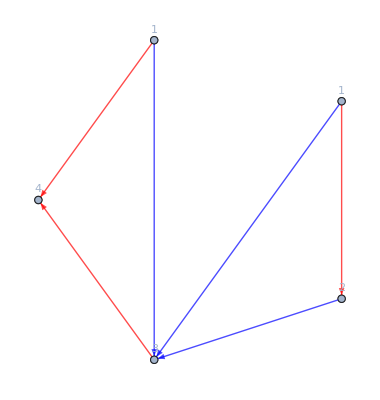
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,False,True,False}

True

Conditions:  {True,False,True,False}

True

No graph survided.

Momenta:  {0,1,1,0}

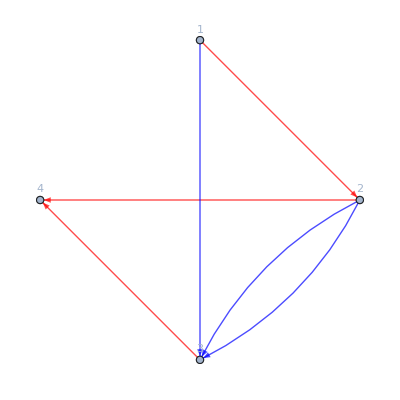
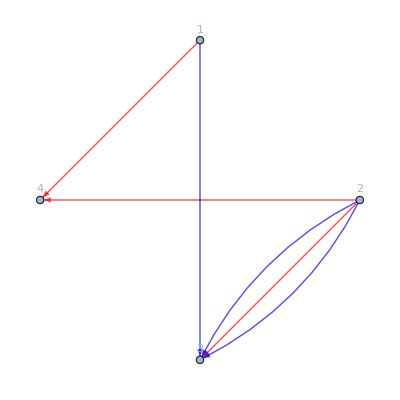
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

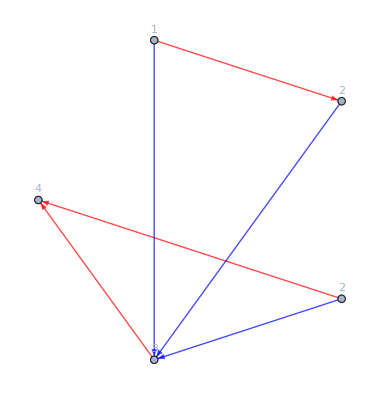
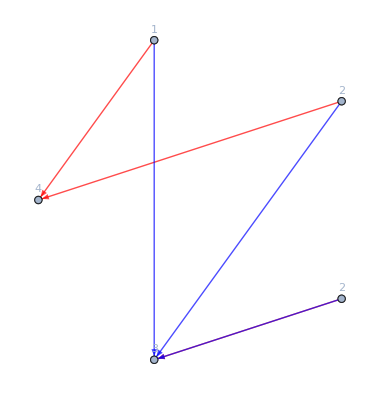
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {False}

False

Graphs:  {-Graphics-}

{12 (43p_2)^2 12,-41 42 33p_2 31 32}

```mathematica
UniformMassStructres[6,Echos->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
```

```mathematica
UniformMassStructres[6,MomentumConservation->False][{1,1,0},{2,1,0},{3,1},{4,-1}]
```

{41 43p_1 22p_1 31,12 (43p_2)^2 12,41 43p_2 22p_1 31,-32 41 43p_1 31 32,34 41 23p_1 31 32,41 42 42p_1 34 31,-41 42 43p_1 32 41,-34 12 43p_2 31 32,-41 42 33p_2 31 32,-41 42 43p_2 32 41,-41 42 43p_2 34 12,34 41 42 34 31 32}

```mathematica
IndependentSpinStructres[6][{1,1,0},{2,1,0},{3,1},{4,-1}]
```

{12 (43p_2)^2 12,-41 42 33p_2 31 32,-41 12 43p_2 1 32,-42 12 43p_2 2 31,-42 43p_2 1 31 12,42^2 2 1 31^2,-41 43p_2 2 32 12,41^2 1 2 32^2}

```mathematica
IndependentSpinStructres[6,MassSquared->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
```

{12 (43p_2)^2 12,-41 42 33p_2 31 32,-41 12 43p_2 1 32,-42 12 43p_2 2 31,-42 43p_2 1 31 12,42^2 2 1 31^2,-41 43p_2 2 32 12,41^2 1 2 32^2,41 42 1 1 31 32,41 42 2 2 31 32}